## Some random reverse engineering attempts

(SSS code not needed for this material, only local commands/functions used, can be run in WolframCloud.)

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

### Code

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
Clear[NetSummary];

Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];

NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];

NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

### Examples

This code displays some “Netsie” form, expands it as specified to a list of Reduced Net Difference Sets, displays the corresponding unreduced form, the network links, and finally a Graph (or Graph3D) display of the network.   (In later examples, only the first two and last are shown.)  To use this file, copy & paste one of the Input cells at the end of the examples section, make changes to the Netsie, and see what sort of network results!  In particular, this is to test various hypotheses about the dimension of networks with particular powers of n in the Netsie.

First, our constructed simple 2-D network:

𝕊_(n=1)^∞[n·{{n,n+1}}]

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}},10·{{10,11}},11·{{11,12}},12·{{12,13}},13·{{13,14}},14·{{14,15}},15·{{15,16}}}

{{1,2},{2,3},{2,3},{3,4},{3,4},«111»,{15,16},{15,16},{15,16},{15,16}}

{1→2,1→3,2→4,2→5,3→5,«230»,118→134,119→134,119→135,120→135,120→136}

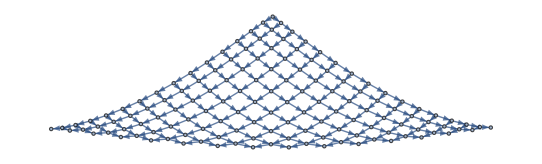

```mathematica
NetSummary[n·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+1}},{n,1,15}]]
FromReducedNetDifferenceSets[%]//Short
FromNetDifferenceSets[%]//Short
Graph[%,GraphLayout->"SpringElectricalEmbedding"]
```

One tweak makes it a cone!  Is this 3-D now?  Maybe not, maybe still 2-D.

```mathematica
NetSummary[(n+1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n+1)·{{n,n+1}},{n,1,20}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n+1)·{{n,n+1}}]

{2·{{1,2}},3·{{2,3}},4·{{3,4}},5·{{4,5}},6·{{5,6}},7·{{6,7}},8·{{7,8}},9·{{8,9}},10·{{9,10}},11·{{10,11}},12·{{11,12}},13·{{12,13}},14·{{13,14}},15·{{14,15}},16·{{15,16}},17·{{16,17}},18·{{17,18}},19·{{18,19}},20·{{19,20}},21·{{20,21}}}

-Graphics3D-

Having 3 connections from each node apparently does not equate to 3-D:

```mathematica
NetSummary[n·{{n,n+1,n+2}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+1,n+2}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n·{{n,n+1,n+2}}]

{1·{{1,2,3}},2·{{2,3,4}},3·{{3,4,5}},4·{{4,5,6}},5·{{5,6,7}},6·{{6,7,8}},7·{{7,8,9}},8·{{8,9,10}},9·{{9,10,11}},10·{{10,11,12}}}

-Graphics3D-

An interesting hybrid:

```mathematica
NetSummary[n·{{n,n+2}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+2}},{n,1,25}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n·{{n,n+2}}]

{1·{{1,3}},2·{{2,4}},3·{{3,5}},4·{{4,6}},5·{{5,7}},6·{{6,8}},7·{{7,9}},8·{{8,10}},9·{{9,11}},10·{{10,12}},11·{{11,13}},12·{{12,14}},13·{{13,15}},14·{{14,16}},15·{{15,17}},16·{{16,18}},17·{{17,19}},18·{{18,20}},19·{{19,21}},20·{{20,22}},21·{{21,23}},22·{{22,24}},23·{{23,25}},24·{{24,26}},25·{{25,27}}}

-Graphics3D-

Try a fixed number of copies:  still 2-D?!

𝕊_(n=1)^∞[2·{{n,n+1}}]

{2·{{1,2}},2·{{2,3}},2·{{3,4}},2·{{4,5}},2·{{5,6}},2·{{6,7}},2·{{7,8}},2·{{8,9}},2·{{9,10}},2·{{10,11}},2·{{11,12}},2·{{12,13}},2·{{13,14}},2·{{14,15}},2·{{15,16}},2·{{16,17}},2·{{17,18}},2·{{18,19}},«14»,2·{{33,34}},2·{{34,35}},2·{{35,36}},2·{{36,37}},2·{{37,38}},2·{{38,39}},2·{{39,40}},2·{{40,41}},2·{{41,42}},2·{{42,43}},2·{{43,44}},2·{{44,45}},2·{{45,46}},2·{{46,47}},2·{{47,48}},2·{{48,49}},2·{{49,50}},2·{{50,51}}}

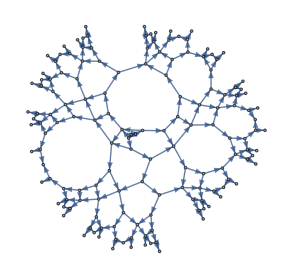

```mathematica
NetSummary[2·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[2·{{n,n+1}},{n,1,50}]]//Short[#,8]&
Graph@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

```mathematica
NetSummary[3·{{n,n+1}},{n,2,∞}]
ExpandAll[NetSummary[3·{{n,n+1}},{n,2,50}]]//Short
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=2)^∞[3·{{n,n+1}}]

{3·{{2,3}},3·{{3,4}},3·{{4,5}},«44»,3·{{49,50}},3·{{50,51}}}

-Graphics3D-

Does n^2·{n...} make it 3-D?  It doesn’t look like it:

```mathematica
NetSummary[n^2·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[n^2·{{n,n+1}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n^2·{{n,1+n}}]

{1·{{1,2}},4·{{2,3}},9·{{3,4}},16·{{4,5}},25·{{5,6}},36·{{6,7}},49·{{7,8}},64·{{8,9}},81·{{9,10}},100·{{10,11}}}

-Graphics3D-

(n-1)·{n...} spirals the opposite direction from (n+1)·{n...}:

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,50}]]//Short
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},«45»,48·{{49,50}},49·{{50,51}}}

-Graphics3D-

Even though the following only has 1 connection (or none!) per graph vertex, it should be considered 2-D:  line up the increasingly long line segments in a row, one direction takes you to the next segment, but the second dimension appears in the increasing lengths.

𝕊_(n=1)^∞[n·{{n}}]

{1·{{1}},2·{{2}},3·{{3}},4·{{4}},5·{{5}},6·{{6}},7·{{7}},8·{{8}},9·{{9}},10·{{10}}}

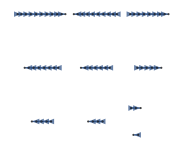

```mathematica
NetSummary[n·{{n}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n}},{n,1,10}]]
Graph[FromNetDifferenceSets@FromReducedNetDifferenceSets@%,GraphLayout->{PackingLayout->"NestedGrid"}]
```

And no, 4 connections doesn’t mean 4-D:

```mathematica
NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,5}]
ExpandAll[NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^5[n·{{n,n+1,n+2,n+3}}]

{1·{{1,2,3,4}},2·{{2,3,4,5}},3·{{3,4,5,6}},4·{{4,5,6,7}},5·{{5,6,7,8}},6·{{6,7,8,9}},7·{{7,8,9,10}},8·{{8,9,10,11}},9·{{9,10,11,12}},10·{{10,11,12,13}}}

-Graphics3D-

### Try finding the dimension algorithmically....

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,100}]]//Short
Graph3D[g1=FromNetDifferenceSets@FromReducedNetDifferenceSets@%]
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},«95»,98·{{99,100}},99·{{100,101}}}

-Graphics3D-

```mathematica
GraphDistance[g1,1]//Short[#,10]&
```

{0,1,1,∞,∞,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,«4847»,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95}

```mathematica
Tally[%]/. {a_,b_}:>b·{a}
```

{1·{0},2·{1},2·{∞},4·{2},6·{3},7·{4},9·{5},10·{6},11·{7},12·{8},13·{9},14·{10},15·{11},17·{12},18·{13},19·{14},20·{15},21·{16},22·{17},23·{18},24·{19},25·{20},26·{21},27·{22},28·{23},29·{24},30·{25},31·{26},33·{27},34·{28},35·{29},36·{30},37·{31},38·{32},39·{33},40·{34},41·{35},42·{36},43·{37},44·{38},45·{39},46·{40},47·{41},48·{42},49·{43},50·{44},51·{45},52·{46},53·{47},54·{48},55·{49},56·{50},57·{51},58·{52},59·{53},60·{54},61·{55},62·{56},63·{57},65·{58},66·{59},67·{60},68·{61},69·{62},70·{63},71·{64},72·{65},73·{66},74·{67},75·{68},76·{69},77·{70},78·{71},79·{72},80·{73},81·{74},82·{75},83·{76},84·{77},85·{78},86·{79},87·{80},88·{81},89·{82},90·{83},91·{84},92·{85},93·{86},94·{87},95·{88},96·{89},97·{90},98·{91},99·{92},100·{93},101·{94},26·{95}}

```mathematica
Subtract[
%261[[6;;-2]] /. n_·{a_}:>{a,n},
%261[[4;;-4]]/. n_·{a_}:>{a,n}] /. {a_,n_}:>n·{a}
```

{3·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2}}

```mathematica
{3·3·{2},5·2·{2},2·3·{2},13·2·{2},2·3·{2},29·2·{2},2·3·{2},(>=36)·2·{2}}
```